```mathematica
b:=Sqrt[(3-r)^2+z^2]; 
ψ=b^2;
F=2(sf+ shear* b^2)Sqrt[3^2-b^2];
```

Ok, those were the definitions. Actually ψ is a conditional expression, and it is zero if b>b_0if it is outside the ring. The cos cubed makes sure that the first and second derivative are zero at the boundary.

```mathematica
Subscript[B, r]  =-1/r  D[ψ,z]
Subscript[B, ϕ]=F/r
Subscript[B, z]= 1/r  D[ψ,r]
```

-(2 z)/r

(2 √(9-(3-r)^2-z^2) (sf+shear ((3-r)^2+z^2)))/r

-(2 (3-r))/r

```mathematica
Div[{Subscript[B, r], Subscript[B, ϕ], Subscript[B, z]}, {r,ϕ,z}, "Cylindrical"] //Simplify
```

0

```mathematica
Subscript[J, 0] =Curl[{Subscript[B, r], 0, Subscript[B, z]}, {r, ϕ, z}, "Cylindrical"]
Plot[J[[2]]/. z-> 0, {r, .5, 1.5}]
```

{0,-(2 (3-r))/r^2-4/r,0}

-Graphics-

```mathematica
fn=Sqrt[{Subscript[B, r], Subscript[B, ϕ], Subscript[B, z]}.{Subscript[B, r], Subscript[B, ϕ], Subscript[B, z]}]/.{ϕ->0, ampl->1, tor->1, bnull->.5}//FullSimplify
ContourPlot[fn/.{ampl->1, tor->1, bnull->.5}, {r,.5,1.5},{z,-.5,.5}]
Plot[fn/.{z-> 0, bnull-> 1/2, tor->5, ampl->1}, {r, .5, 1.5}]
Subscript[B, ϕ]/.{z-> 0, bnull-> 1/2, tor->5, ampl->1}
```

2 √(((-3+r)^2+z^2-((-6+r) r+z^2) (sf+shear ((-3+r)^2+z^2))^2)/r^2)

-Graphics-

-Graphics-

(2 √(9-(3-r)^2) (sf+(3-r)^2 shear))/r

```mathematica
Subscript[B, cart]=TransformedField["Cylindrical"-> "Cartesian", {Subscript[B, r],Subscript[B, ϕ], Subscript[B, z]}, {r, ϕ, z}-> {x, y, zz}]//Simplify
```

{(2 (-x zz-y √(-x^2-y^2+6 √(x^2+y^2)-zz^2) (sf+shear ((-3+√(x^2+y^2))^2+zz^2))))/(x^2+y^2),(2 (-y zz+x √(-x^2-y^2+6 √(x^2+y^2)-zz^2) (sf+shear ((-3+√(x^2+y^2))^2+zz^2))))/(x^2+y^2),2-6/(√(x^2+y^2))}

```mathematica
bla=Div[TransformedField["Cylindrical"-> "Cartesian", {Subscript[B, r],Subscript[B, ϕ], Subscript[B, z]}, {r, ϕ, z}-> {x, y, zz}], {x, y, zz}]//Simplify
```

0

```mathematica
0
```

0

```mathematica
FortranForm[Subscript[B, cart][[1]]/.{x->xx[0], y->xx[1], zz-> xx[2]}]
```

(2*(-(xx(0)*xx(2)) - xx(1)*Sqrt(-xx(0)**2 - xx(1)**2 + 6*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*(sf + shear*((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2))))/(xx(0)**2 + xx(1)**2)

```mathematica
FortranForm[Subscript[B, cart][[2]]/.{x->xx[0], y->xx[1], zz-> xx[2]}]
```

(2*(-(xx(1)*xx(2)) + xx(0)*Sqrt(-xx(0)**2 - xx(1)**2 + 6*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*(sf + shear*((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2))))/(xx(0)**2 + xx(1)**2)

```mathematica
FortranForm[Subscript[B, cart][[3]]/.{x->xx[0], y->xx[1], zz-> xx[2]}]
```

2 - 6/Sqrt(xx(0)**2 + xx(1)**2)

```mathematica
$Assumptions :={a∈ Reals, a>0, a<1}
Subscript[B, pr]=-D[ψ, r]/. {z->0, r->3+a}//Simplify
```

-2 a

```mathematica
Subscript[B, ϕr]=F/. {z->0, r->3+a}//Simplify
```

2 √(9-a^2) (sf+a^2 shear)

```mathematica
Tintegral = Integrate[a/(3+a Cos[θ]), {θ, 0, 2π}]//Simplify
```

(2 a π)/(√(9-a^2))

```mathematica
q= 1/(2π)Subscript[B, ϕr]/Subscript[B, pr] Tintegral/.{shear->1, sf->2/3}//Simplify
```

-2/3-a^2

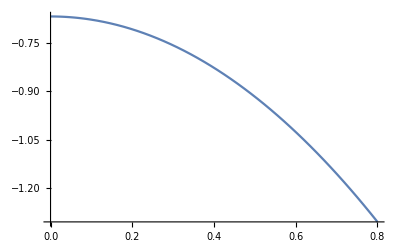

```mathematica
Plot[q/.{ampl-> 1, shear->1, sf->3/2}, {a, 0, .8}]
```

```mathematica
i=1/q
```

1/(-2/3-a^2)

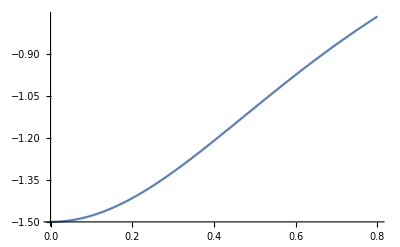

```mathematica
Plot[i/.{ampl-> 1}, {a, 0,.8}]
```

```mathematica
1/q/.a-> .5
```

-1.09091

```mathematica
``
```

```mathematica
Subscript[ψ, pc]= 1/(2π d^2)Exp[-b^2/(2 d^2)]((r-3)+ⅈ z )^2 Exp[ⅈ*3ϕ]
```

(ⅇ^(-((3-r)^2+z^2)/(2 d^2)+3 ⅈ ϕ) (-3+r+ⅈ z)^2)/(2 d^2 π)

```mathematica
Subscript[B, rpc]  =-1/r  D[Subscript[ψ, pc],z]
Subscript[B, zpc]= 1/r  D[Subscript[ψ, pc],r]
```

-((ⅈ ⅇ^(-((3-r)^2+z^2)/(2 d^2)+3 ⅈ ϕ) (-3+r+ⅈ z))/(d^2 π)-(ⅇ^(-((3-r)^2+z^2)/(2 d^2)+3 ⅈ ϕ) (-3+r+ⅈ z)^2 z)/(2 d^4 π))/r

((ⅇ^(-((3-r)^2+z^2)/(2 d^2)+3 ⅈ ϕ) (-3+r+ⅈ z))/(d^2 π)+(ⅇ^(-((3-r)^2+z^2)/(2 d^2)+3 ⅈ ϕ) (3-r) (-3+r+ⅈ z)^2)/(2 d^4 π))/r

```mathematica
Subscript[B, rp]=Re[Subscript[B, rpc]]//ComplexExpand//FullSimplify
Subscript[B, zp]=Re[Subscript[B, zpc]]//ComplexExpand//FullSimplify
```

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) (z (2 d^2+(-3+r)^2-z^2) Cos[3 ϕ]+2 (-3+r) (d-z) (d+z) Sin[3 ϕ]))/(2 d^4 π r)

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) ((-3+r) (2 d^2-(-3+r)^2+z^2) Cos[3 ϕ]-2 (3+d-r) (-3+d+r) z Sin[3 ϕ]))/(2 d^4 π r)

```mathematica
Subscript[B, pcart]= TransformedField["Cylindrical"-> "Cartesian", {Subscript[B, rp],0, Subscript[B, zp]}, {r, ϕ, z}-> {x, y, zz}]//FullSimplify
```

{(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) x (zz (2 d^2+(-3+√(x^2+y^2))^2-zz^2) Cos[3 ArcTan[x,y]]+2 (-3+√(x^2+y^2)) (d-zz) (d+zz) Sin[3 ArcTan[x,y]]))/(2 d^4 π (x^2+y^2)),(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) y (zz (2 d^2+(-3+√(x^2+y^2))^2-zz^2) Cos[3 ArcTan[x,y]]+2 (-3+√(x^2+y^2)) (d-zz) (d+zz) Sin[3 ArcTan[x,y]]))/(2 d^4 π (x^2+y^2)),(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) ((-3+√(x^2+y^2)) (2 d^2-(-3+√(x^2+y^2))^2+zz^2) Cos[3 ArcTan[x,y]]+2 (9-d^2+x^2+y^2-6 √(x^2+y^2)) zz Sin[3 ArcTan[x,y]]))/(2 d^4 π √(x^2+y^2))}

```mathematica
FortranForm[Subscript[B, pcart][[1]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(xx(0)*(2*Sin(3*ArcTan(xx(0),xx(1)))*(-3 + Sqrt(xx(0)**2 + xx(1)**2))*(width - xx(2))*(width + xx(2)) + Cos(3*ArcTan(xx(0),xx(1)))*xx(2)*(2*width**2 + (-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 - xx(2)**2)))/
     -  (2.*E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*Pi*width**4*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[Subscript[B, pcart][[2]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width }]
```

(xx(1)*(2*Sin(3*ArcTan(xx(0),xx(1)))*(-3 + Sqrt(xx(0)**2 + xx(1)**2))*(width - xx(2))*(width + xx(2)) + Cos(3*ArcTan(xx(0),xx(1)))*xx(2)*(2*width**2 + (-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 - xx(2)**2)))/
     -  (2.*E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*Pi*width**4*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[Subscript[B, pcart][[3]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(2*Sin(3*ArcTan(xx(0),xx(1)))*(9 - width**2 + xx(0)**2 + xx(1)**2 - 6*Sqrt(xx(0)**2 + xx(1)**2))*xx(2) + 
     -    Cos(3*ArcTan(xx(0),xx(1)))*(-3 + Sqrt(xx(0)**2 + xx(1)**2))*(2*width**2 - (-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2))/
     -  (2.*E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*Pi*width**4*Sqrt(xx(0)**2 + xx(1)**2))

(ⅇ^(-(9+x^2-6 √(x^2)+zz^2)/d^2) (zz^2 (2 d^2+(-3+√(x^2))^2-zz^2)^2+(-3+√(x^2))^2 (2 d^2-(-3+√(x^2))^2+zz^2)^2))/(4 d^8 π^2 x^2)

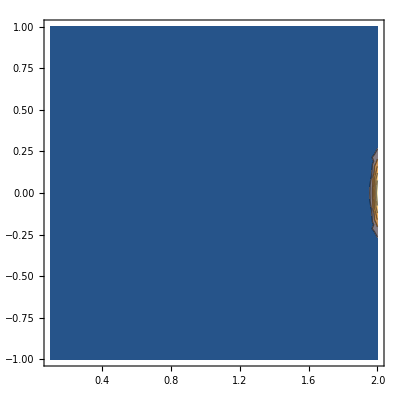

```mathematica
fn2 = Subscript[B, pcart].Subscript[B, pcart]/.{y->0 }//FullSimplify
ContourPlot[fn2/.{d->0.2}, {x,0.1,2},{zz,-1,1}, PlotRange->Full]
```

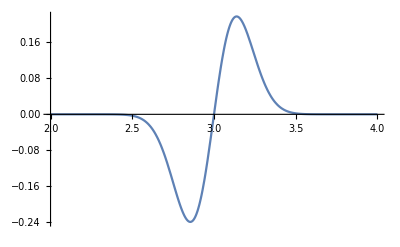

```mathematica
Plot[Subscript[B, pcart][[1]]/.{d-> .2, zz->x-3, y->0}, {x, 2,4}, PlotRange->Full]
```

3.97887 Re[ⅇ^(-12.5 ((3-r)^2+z^2)+3 ⅈ ϕ) (-3+r+ⅈ z)^2]

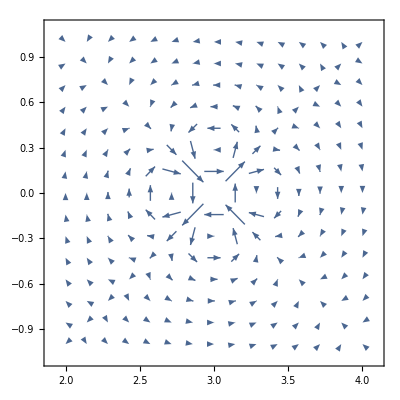

```mathematica
fn=Re[Subscript[ψ, pc]]/.{ d->.2}
VectorPlot[{Subscript[B, pcart][[1]]/.{d->.2, y->0},Subscript[B, pcart][[3]]/.{d->.2, y->0}}, {x,2,4},{zz,-1,1}, PlotRange->Full]
Manipulate[ContourPlot[fn/.{ϕ->a}, {r,2,4},{z,-1,1}, PlotRange->Full], {a, 0, 2π}]
```

```mathematica
bla = Div[Subscript[B, pcart], {x, y, zz}]
Plot[Bla/.{y->0,zz->0, d-> .1}, {x,0, 2}]
```

(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) y ((2 x y (-1+√(x^2+y^2)) zz)/(√(x^2+y^2))+(2 y^2 (-d+zz) (d+zz))/(√(x^2+y^2))+2 (-1+√(x^2+y^2)) (-d+zz) (d+zz)))/(d^2 (x^2+y^2)^(3/2))+(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) (-2 y (3-d^2+x^2+y^2-4 √(x^2+y^2))-x (-3+√(x^2+y^2)) (-1+√(x^2+y^2)-zz)+x (-3+√(x^2+y^2)) (-1+√(x^2+y^2)+zz)))/(d^2 (x^2+y^2))-(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) zz (2 d^2 x (-1+√(x^2+y^2))-2 y (3-d^2+x^2+y^2-4 √(x^2+y^2)) zz-x (-3+√(x^2+y^2)) (-1+√(x^2+y^2)-zz) (-1+√(x^2+y^2)+zz)))/(d^4 (x^2+y^2))+(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) x ((2 x^2 (-1+√(x^2+y^2)) zz)/(√(x^2+y^2))+(2 x y (-d+zz) (d+zz))/(√(x^2+y^2))+zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2)))/(d^2 (x^2+y^2)^(3/2))-(3 ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) x^2 (2 y (-1+√(x^2+y^2)) (-d+zz) (d+zz)+x zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2)))/(d^2 (x^2+y^2)^(5/2))-(3 ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) y^2 (2 y (-1+√(x^2+y^2)) (-d+zz) (d+zz)+x zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2)))/(d^2 (x^2+y^2)^(5/2))+(2 ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) (2 y (-1+√(x^2+y^2)) (-d+zz) (d+zz)+x zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2)))/(d^2 (x^2+y^2)^(3/2))-(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) x^2 (-3+√(x^2+y^2)) (2 y (-1+√(x^2+y^2)) (-d+zz) (d+zz)+x zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2)))/(d^4 (x^2+y^2)^2)-(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) y^2 (-3+√(x^2+y^2)) (2 y (-1+√(x^2+y^2)) (-d+zz) (d+zz)+x zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2)))/(d^4 (x^2+y^2)^2)

-Graphics-

## Forces section

```mathematica
Subscript[F, 01]=Cross[Subscript[J, 0], {Subscript[B, rp], 0, Subscript[B, zp]}]//Simplify
VectorPlot[{Subscript[F, 01][[1]]/.{d->.1, ϕ->0}, Subscript[F, 01][[3]]/.{d->.1, ϕ-> 0}}, {r, .5, 1.5}, {z, -.5, .5}]
```

{(2 ⅇ^(-(9-6 r+r^2+z^2)/(2 d^2)) (3+r) ((2 d^2 (-1+r)-(-3+r) (1-2 r+r^2-z^2)) Cos[ϕ]+2 (-3+d^2+4 r-r^2) z Sin[ϕ]))/(d^2 r^3),0,-(2 ⅇ^(-(9-6 r+r^2+z^2)/(2 d^2)) (3+r) (-z (-1-2 d^2+2 r-r^2+z^2) Cos[ϕ]-2 (-1+r) (d^2-z^2) Sin[ϕ]))/(d^2 r^3)}

Part::partw: Part 3 of ((0.+4.69023 ⅈ) (sf+6.49957 shear))_1 does not exist.

Part::partw: Part 3 of ((0.+4.53764 ⅈ) (sf+6.14754 shear))_1 does not exist.

Part::partw: Part 3 of ((0.+4.38439 ⅈ) (sf+5.80571 shear))_1 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

√((4 ⅇ^(-(9-6 r+r^2+z^2)/d^2) (3+r)^2 ((2 d^2 (-1+r)-(-3+r) (1-2 r+r^2-z^2)) Cos[ϕ]+2 (-3+d^2+4 r-r^2) z Sin[ϕ])^2)/(d^4 r^6)+(4 ⅇ^(-(9-6 r+r^2+z^2)/d^2) (3+r)^2 (-z (-1-2 d^2+2 r-r^2+z^2) Cos[ϕ]-2 (-1+r) (d^2-z^2) Sin[ϕ])^2)/(d^4 r^6))

√((40000. ⅇ^(-100. (9-6 r+r^2+z^2)) (3+r)^2 z^2 (-1.02+2 r-r^2+z^2)^2)/r^6+(40000. ⅇ^(-100. (9-6 r+r^2+z^2)) (3+r)^2 (0.02 (-1+r)-(-3+r) (1-2 r+r^2-z^2))^2)/r^6)

-Graphics-

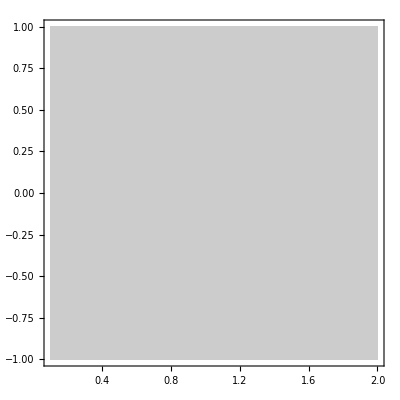

```mathematica
Subscript[F, 01r]= Sqrt[(Subscript[F, 01][[1]])^2+ (Subscript[F, 01][[3]])^2]
bla = Subscript[F, 01r]/.{d->.1, ϕ-> 0}
ContourPlot[Subscript[F, 01r]/.{d->.1, ϕ-> 1}, {r, .5, 1.5}, {z, -.5, .5}, PlotRange-> Full]
ContourPlot[bla, {r,0.1,2},{z,-1,1}, PlotRange->Full]
```

```mathematica
Subscript[J, 1]= Curl[{Subscript[B, rp], 0, Subscript[B, zp]}, {r, ϕ, z}, "Cylindrical"]//Simplify
Subscript[F, 10]= Cross[Subscript[J, 1], {Subscript[B, r], Subscript[B, ϕ], Subscript[B, z]}]//Simplify
VectorPlot[{Subscript[F, 10][[1]]/.{d->.1, ϕ->0}, Subscript[F, 10][[3]]/.{d->.1, ϕ-> 0}}, {r, .5, 1.5}, {z, -.5, .5}]
```

{(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) (2 (-3+d^2+4 r-r^2) z Cos[ϕ]+(-2 d^2 (-1+r)+(-3+r) (1-2 r+r^2-z^2)) Sin[ϕ]))/(d^2 r^2),(ⅇ^(-(9-6 r+r^2+z^2)/(2 d^2)) ((2 d^4 (-1+r)+d^2 (3-15 r^2+5 r^3-3 z^2+r (7-5 z^2))+r (-9-22 r^2+8 r^3-r^4+8 z^2+z^4-4 r (-6+z^2))) Cos[ϕ]+2 z (d^4+d^2 (-3-6 r+5 r^2)-(-1+r) r (9-6 r+r^2+z^2)) Sin[ϕ]))/(d^4 r^2),-(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) (2 (-1+r) (-d+z) (d+z) Cos[ϕ]-z (2 d^2+(-1+r)^2-z^2) Sin[ϕ]))/(d^2 r^2)}

{-1/(d^4 r^3)2 ⅇ^(-(9-6 r+r^2+z^2)/(2 d^2)) ((2 d^4 (-1+r) (-3+r+sf √(-8+6 r-r^2-z^2)+9 shear √(-8+6 r-r^2-z^2)-6 r shear √(-8+6 r-r^2-z^2)+r^2 shear √(-8+6 r-r^2-z^2)+shear z^2 √(-8+6 r-r^2-z^2))-(-3+r) r (9+22 r^2-8 r^3+r^4-8 z^2-z^4+4 r (-6+z^2))+d^2 (-9+5 r^4+2 shear z^4 √(-8+6 r-r^2-z^2)+z^2 (9+2 sf √(-8+6 r-r^2-z^2)+18 shear √(-8+6 r-r^2-z^2))-2 r^3 (15+shear z^2 √(-8+6 r-r^2-z^2))+r^2 (52+z^2 (-5+14 shear √(-8+6 r-r^2-z^2)))-2 r (9+shear z^4 √(-8+6 r-r^2-z^2)+z^2 (-6+sf √(-8+6 r-r^2-z^2)+15 shear √(-8+6 r-r^2-z^2))))) Cos[ϕ]+z (-2 r (3-4 r+r^2) (9-6 r+r^2+z^2)+2 d^4 (-3+r+sf √(-8+6 r-r^2-z^2)+9 shear √(-8+6 r-r^2-z^2)-6 r shear √(-8+6 r-r^2-z^2)+r^2 shear √(-8+6 r-r^2-z^2)+shear z^2 √(-8+6 r-r^2-z^2))+d^2 (18+sf √(-8+6 r-r^2-z^2)+9 shear √(-8+6 r-r^2-z^2)+r^4 shear √(-8+6 r-r^2-z^2)-sf z^2 √(-8+6 r-r^2-z^2)-8 shear z^2 √(-8+6 r-r^2-z^2)-shear z^4 √(-8+6 r-r^2-z^2)+r^3 (10-8 shear √(-8+6 r-r^2-z^2))+r^2 (-42+sf √(-8+6 r-r^2-z^2)+22 shear √(-8+6 r-r^2-z^2))+r (30-2 sf √(-8+6 r-r^2-z^2)+4 shear √(-8+6 r-r^2-z^2) (-6+z^2)))) Sin[ϕ]),-(2 ⅇ^(-(9-6 r+r^2+z^2)/(2 d^2)) (2 z (-2 d^2 (-2+r)+(-1+r) (9-6 r+r^2+z^2)) Cos[ϕ]+(-9-22 r^2+8 r^3-r^4+8 z^2+z^4+2 d^2 (3-4 r+r^2-z^2)-4 r (-6+z^2)) Sin[ϕ]))/(d^2 r^3),1/(d^4 r^3)2 ⅇ^(-(9-6 r+r^2+z^2)/(2 d^2)) (z (r (9+22 r^2-8 r^3+r^4-8 z^2-z^4+4 r (-6+z^2))+2 d^4 (1+sf √(-8+6 r-r^2-z^2)+9 shear √(-8+6 r-r^2-z^2)+r^2 shear √(-8+6 r-r^2-z^2)+shear z^2 √(-8+6 r-r^2-z^2)-r (1+6 shear √(-8+6 r-r^2-z^2)))-d^2 (3-3 z^2+6 sf √(-8+6 r-r^2-z^2)+54 shear √(-8+6 r-r^2-z^2)+2 r^4 shear √(-8+6 r-r^2-z^2)+6 shear z^2 √(-8+6 r-r^2-z^2)+r^3 (5-20 shear √(-8+6 r-r^2-z^2))+r^2 (-15+2 sf √(-8+6 r-r^2-z^2)+2 shear √(-8+6 r-r^2-z^2) (36+z^2))-r (-7+8 sf √(-8+6 r-r^2-z^2)+108 shear √(-8+6 r-r^2-z^2)+z^2 (5+8 shear √(-8+6 r-r^2-z^2))))) Cos[ϕ]+(2 (-1+r) r z^2 (9-6 r+r^2+z^2)-2 d^4 ((-1+r) (sf+(-3+r)^2 shear) √(-8+6 r-r^2-z^2)+z^2 (1+(-1+r) shear √(-8+6 r-r^2-z^2)))+d^2 ((-3+r) (-1+r)^2 (sf+(-3+r)^2 shear) √(-8+6 r-r^2-z^2)-(-3+r) shear z^4 √(-8+6 r-r^2-z^2)+z^2 (2 r^2 (-5+2 shear √(-8+6 r-r^2-z^2))+3 (2+sf √(-8+6 r-r^2-z^2)+8 shear √(-8+6 r-r^2-z^2))-r (-12+sf √(-8+6 r-r^2-z^2)+20 shear √(-8+6 r-r^2-z^2))))) Sin[ϕ])}

Part::partw: Part 3 of ((0.+4.69023 ⅈ) (sf+6.49957 shear))_10 does not exist.

Part::partw: Part 3 of ((0.+4.53764 ⅈ) (sf+6.14754 shear))_10 does not exist.

Part::partw: Part 3 of ((0.+4.38439 ⅈ) (sf+5.80571 shear))_10 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Subscript[ψ, pc1]= Exp[-b^2/(2 d^2)]((r-1)+ⅈ z ) Exp[-ⅈ*ϕ]
```

ⅇ^(-((3-r)^2+z^2)/(2 d^2)-ⅈ ϕ) (-1+r+ⅈ z)

```mathematica
Subscript[B, rpc1]  =-1/r  D[Subscript[ψ, pc1],z]
Subscript[B, zpc1]= 1/r  D[Subscript[ψ, pc1],r]
```

-(ⅈ ⅇ^(-((3-r)^2+z^2)/(2 d^2)-ⅈ ϕ)-(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-ⅈ ϕ) (-1+r+ⅈ z) z)/d^2)/r

(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-ⅈ ϕ)+(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-ⅈ ϕ) (3-r) (-1+r+ⅈ z))/d^2)/r

```mathematica
Subscript[B, rp1]=Re[Subscript[B, rpc1]]//ComplexExpand//FullSimplify
Subscript[B, zp1]=Re[Subscript[B, zpc1]]//ComplexExpand//FullSimplify
```

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) ((-1+r) z Cos[ϕ]+(-d+z) (d+z) Sin[ϕ]))/(d^2 r)

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) ((d^2-(-3+r) (-1+r)) Cos[ϕ]-(-3+r) z Sin[ϕ]))/(d^2 r)

```mathematica
Subscript[B, pcart1]= TransformedField["Cylindrical"-> "Cartesian", {Subscript[B, rp1],0, Subscript[B, zp1]}, {r, ϕ, z}-> {x, y, zz}]//FullSimplify
```

{(ⅇ^(-(9+x^2+y^2-6 √(x^2+y^2)+zz^2)/(2 d^2)) x (-d^2 y+zz (x (-1+√(x^2+y^2))+y zz)))/(d^2 (x^2+y^2)^(3/2)),(ⅇ^(-(9+x^2+y^2-6 √(x^2+y^2)+zz^2)/(2 d^2)) y (-d^2 y+zz (x (-1+√(x^2+y^2))+y zz)))/(d^2 (x^2+y^2)^(3/2)),(ⅇ^(-(9+x^2+y^2-6 √(x^2+y^2)+zz^2)/(2 d^2)) (-x^3+x (-3+d^2-y^2+4 √(x^2+y^2))-y (-3+√(x^2+y^2)) zz))/(d^2 (x^2+y^2))}

```mathematica
FortranForm[Subscript[B, pcart1][[1]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(xx(0)*(-(width**2*xx(1)) + xx(2)*(xx(0)*(-1 + Sqrt(xx(0)**2 + xx(1)**2)) + xx(1)*xx(2))))/
     -  (E**((9 + xx(0)**2 + xx(1)**2 - 6*Sqrt(xx(0)**2 + xx(1)**2) + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2)**1.5)

```mathematica
FortranForm[Subscript[B, pcart1][[2]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width }]
```

(xx(1)*(-(width**2*xx(1)) + xx(2)*(xx(0)*(-1 + Sqrt(xx(0)**2 + xx(1)**2)) + xx(1)*xx(2))))/
     -  (E**((9 + xx(0)**2 + xx(1)**2 - 6*Sqrt(xx(0)**2 + xx(1)**2) + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2)**1.5)

```mathematica
FortranForm[Subscript[B, pcart1][[3]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(-xx(0)**3 + xx(0)*(-3 + width**2 - xx(1)**2 + 4*Sqrt(xx(0)**2 + xx(1)**2)) - xx(1)*(-3 + Sqrt(xx(0)**2 + xx(1)**2))*xx(2))/
     -  (E**((9 + xx(0)**2 + xx(1)**2 - 6*Sqrt(xx(0)**2 + xx(1)**2) + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2))

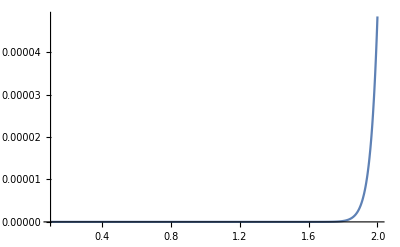

```mathematica
Plot[Subscript[B, pcart1][[3]]/.{d-> .2, zz->0, y->0}, {x, .1,2}, PlotRange->Full]
```

Re[ⅇ^(-12.5 ((3-r)^2+z^2)-ⅈ ϕ) (-1+r+ⅈ z)]

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

{(25. ⅇ^(-12.5 ((-3+√(x^2))^2+zz^2)) zz (0.08+(-1+√(x^2))^2-zz^2) 1⟦1⟧)/(√(x^2)),(0. zz (0.08+(-1+√(x^2))^2-zz^2) 1⟦1⟧)/((x^2)^(3/2)),(25. ⅇ^(-12.5 ((-3+√(x^2))^2+zz^2)) (0.08 x (-1+√(x^2))-x (-3+√(x^2)) (-1+√(x^2)-zz) (-1+√(x^2)+zz)) 1⟦1⟧)/x^2}

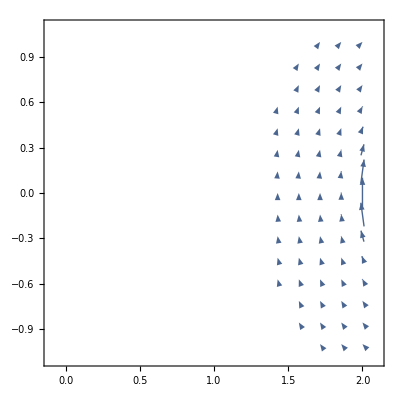

```mathematica
fn=Re[Subscript[ψ, pc1]]/.{ d->.2}
Subscript[B, pcart] 1[[1]]/.{d->.2, y->0}
VectorPlot[{Subscript[B, pcart1][[1]]/.{d->.2, y->0},Subscript[B, pcart1][[3]]/.{d->.2, y->0}}, {x,0,2},{zz,-1,1}, PlotRange->Full]
Manipulate[ContourPlot[fn/.{ϕ->b}, {r,0,2},{z,-1,1}, PlotRange->Full], {b, 0, 2π}]
```

```mathematica
Subscript[ψ, pc33]= Exp[-b^2/(2 d^2)]((r-1)+ⅈ z )^3 Exp[-ⅈ*3ϕ]
```

ⅇ^(-((3-r)^2+z^2)/(2 d^2)-3 ⅈ ϕ) (-1+r+ⅈ z)^3

```mathematica
Subscript[B, rpc33]  =-1/r  D[Subscript[ψ, pc33],z]
Subscript[B, zpc33]= 1/r  D[Subscript[ψ, pc33],r]
```

-(3 ⅈ ⅇ^(-((3-r)^2+z^2)/(2 d^2)-3 ⅈ ϕ) (-1+r+ⅈ z)^2-(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-3 ⅈ ϕ) (-1+r+ⅈ z)^3 z)/d^2)/r

(3 ⅇ^(-((3-r)^2+z^2)/(2 d^2)-3 ⅈ ϕ) (-1+r+ⅈ z)^2+(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-3 ⅈ ϕ) (3-r) (-1+r+ⅈ z)^3)/d^2)/r

```mathematica
Subscript[B, rpc33]=Re[Subscript[B, rpc33]]//ComplexExpand//FullSimplify
Subscript[B, zpc33]=Re[Subscript[B, zpc33]]//ComplexExpand//FullSimplify
```

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) ((-1+r) z (6 d^2+(-1+r)^2-3 z^2) Cos[3 ϕ]-(3 d^2 (-1+r)^2-3 (d^2+(-1+r)^2) z^2+z^4) Sin[3 ϕ]))/(d^2 r)

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) ((-(-3+r) (-1+r) ((-1+r)^2-3 z^2)+3 d^2 ((-1+r)^2-z^2)) Cos[3 ϕ]+z (6 d^2 (-1+r)+(-3+r) (-3 (-1+r)^2+z^2)) Sin[3 ϕ]))/(d^2 r)

```mathematica
Subscript[B, pcart13]= TransformedField["Cylindrical"-> "Cartesian", {Subscript[B, rpc33],0, Subscript[B, zpc33]}, {r, ϕ, z}-> {x, y, zz}]//FullSimplify
```

{(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) x ((-1+√(x^2+y^2)) zz (6 d^2+(-1+√(x^2+y^2))^2-3 zz^2) Cos[3 ArcTan[x,y]]-(3 d^2 (-1+√(x^2+y^2))^2-3 (d^2+(-1+√(x^2+y^2))^2) zz^2+zz^4) Sin[3 ArcTan[x,y]]))/(d^2 (x^2+y^2)),(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) y ((-1+√(x^2+y^2)) zz (6 d^2+(-1+√(x^2+y^2))^2-3 zz^2) Cos[3 ArcTan[x,y]]-(3 d^2 (-1+√(x^2+y^2))^2-3 (d^2+(-1+√(x^2+y^2))^2) zz^2+zz^4) Sin[3 ArcTan[x,y]]))/(d^2 (x^2+y^2)),(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) ((-(-3+√(x^2+y^2)) (-1+√(x^2+y^2)) ((-1+√(x^2+y^2))^2-3 zz^2)+3 d^2 ((-1+√(x^2+y^2))^2-zz^2)) Cos[3 ArcTan[x,y]]+zz (6 d^2 (-1+√(x^2+y^2))+(-3+√(x^2+y^2)) (-3 (-1+√(x^2+y^2))^2+zz^2)) Sin[3 ArcTan[x,y]]))/(d^2 √(x^2+y^2))}

```mathematica
FortranForm[Subscript[B, pcart13][[1]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(xx(0)*(Cos(3*ArcTan(xx(0),xx(1)))*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*xx(2)*(6*width**2 + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - 3*xx(2)**2) - 
     -      Sin(3*ArcTan(xx(0),xx(1)))*(3*width**2*(-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - 3*(width**2 + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2)*xx(2)**2 + xx(2)**4)))/
     -  (E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[Subscript[B, pcart13][[2]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width }]
```

(xx(1)*(Cos(3*ArcTan(xx(0),xx(1)))*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*xx(2)*(6*width**2 + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - 3*xx(2)**2) - 
     -      Sin(3*ArcTan(xx(0),xx(1)))*(3*width**2*(-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - 3*(width**2 + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2)*xx(2)**2 + xx(2)**4)))/
     -  (E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[Subscript[B, pcart13][[3]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(Cos(3*ArcTan(xx(0),xx(1)))*(-((-3 + Sqrt(xx(0)**2 + xx(1)**2))*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - 3*xx(2)**2)) + 
     -       3*width**2*((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - xx(2)**2)) + Sin(3*ArcTan(xx(0),xx(1)))*xx(2)*
     -     (6*width**2*(-1 + Sqrt(xx(0)**2 + xx(1)**2)) + (-3 + Sqrt(xx(0)**2 + xx(1)**2))*(-3*(-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)))/
     -  (E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*width**2*Sqrt(xx(0)**2 + xx(1)**2))

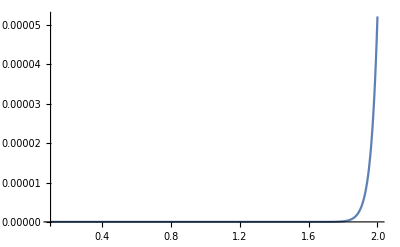

```mathematica
Plot[Subscript[B, pcart13][[3]]/.{d-> .2, zz->0, y->0}, {x, .1,2}, PlotRange->Full]
```

Re[ⅇ^(-12.5 ((3-r)^2+z^2)-3 ⅈ ϕ) (-1+r+ⅈ z)^3]

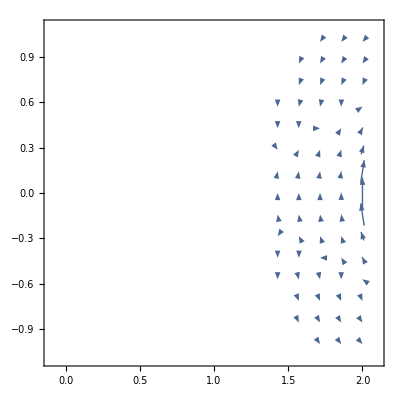

```mathematica
fn=Re[Subscript[ψ, pc33]]/.{ d->.2}
VectorPlot[{Subscript[B, pcart13][[1]]/.{d->.2, y->0},Subscript[B, pcart13][[3]]/.{d->.2, y->0}}, {x,0,2},{zz,-1,1}, PlotRange->Full]
Manipulate[ContourPlot[fn/.{ϕ->b}, {r,0,2},{z,-1,1}, PlotRange->Full], {b, 0, 2π}]
```

```mathematica
Subscript[ψ, pc22]= Exp[-b^2/(2 d^2)]((r-1)+ⅈ z )^2 Exp[-ⅈ*2ϕ]
```

ⅇ^(-((3-r)^2+z^2)/(2 d^2)-2 ⅈ ϕ) (-1+r+ⅈ z)^2

```mathematica
Subscript[B, rpc22]  =-1/r  D[Subscript[ψ, pc22],z]
Subscript[B, zpc22]= 1/r  D[Subscript[ψ, pc22],r]
```

-(2 ⅈ ⅇ^(-((3-r)^2+z^2)/(2 d^2)-2 ⅈ ϕ) (-1+r+ⅈ z)-(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-2 ⅈ ϕ) (-1+r+ⅈ z)^2 z)/d^2)/r

(2 ⅇ^(-((3-r)^2+z^2)/(2 d^2)-2 ⅈ ϕ) (-1+r+ⅈ z)+(ⅇ^(-((3-r)^2+z^2)/(2 d^2)-2 ⅈ ϕ) (3-r) (-1+r+ⅈ z)^2)/d^2)/r

```mathematica
Subscript[B, rpc22]=Re[Subscript[B, rpc22]]//ComplexExpand//FullSimplify
Subscript[B, zpc22]=Re[Subscript[B, zpc22]]//ComplexExpand//FullSimplify
```

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) (z (2 d^2+(-1+r)^2-z^2) Cos[2 ϕ]+2 (-1+r) (-d+z) (d+z) Sin[2 ϕ]))/(d^2 r)

(ⅇ^(-((-3+r)^2+z^2)/(2 d^2)) ((2 d^2 (-1+r)-(-3+r) ((-1+r)^2-z^2)) Cos[2 ϕ]+2 (d^2-(-3+r) (-1+r)) z Sin[2 ϕ]))/(d^2 r)

```mathematica
Subscript[B, pcart22]= TransformedField["Cylindrical"-> "Cartesian", {Subscript[B, rpc22],0, Subscript[B, zpc22]}, {r, ϕ, z}-> {x, y, zz}]//FullSimplify
```

{(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) x (zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2) Cos[2 ArcTan[x,y]]+2 (-1+√(x^2+y^2)) (-d+zz) (d+zz) Sin[2 ArcTan[x,y]]))/(d^2 (x^2+y^2)),(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) y (zz (2 d^2+(-1+√(x^2+y^2))^2-zz^2) Cos[2 ArcTan[x,y]]+2 (-1+√(x^2+y^2)) (-d+zz) (d+zz) Sin[2 ArcTan[x,y]]))/(d^2 (x^2+y^2)),(ⅇ^(-((-3+√(x^2+y^2))^2+zz^2)/(2 d^2)) ((2 d^2 (-1+√(x^2+y^2))-(-3+√(x^2+y^2)) ((-1+√(x^2+y^2))^2-zz^2)) Cos[2 ArcTan[x,y]]+2 (-3+d^2-x^2-y^2+4 √(x^2+y^2)) zz Sin[2 ArcTan[x,y]]))/(d^2 √(x^2+y^2))}

```mathematica
FortranForm[Subscript[B, pcart22][[1]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(xx(0)*(2*Sin(2*ArcTan(xx(0),xx(1)))*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*(-width + xx(2))*(width + xx(2)) + Cos(2*ArcTan(xx(0),xx(1)))*xx(2)*(2*width**2 + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - xx(2)**2)))/
     -  (E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[Subscript[B, pcart22][[2]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width }]
```

(xx(1)*(2*Sin(2*ArcTan(xx(0),xx(1)))*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*(-width + xx(2))*(width + xx(2)) + Cos(2*ArcTan(xx(0),xx(1)))*xx(2)*(2*width**2 + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - xx(2)**2)))/
     -  (E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*width**2*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[Subscript[B, pcart22][[3]]/.{x-> xx[0], y-> xx[1], zz->xx[2], d->width}]
```

(2*Sin(2*ArcTan(xx(0),xx(1)))*(-3 + width**2 - xx(0)**2 - xx(1)**2 + 4*Sqrt(xx(0)**2 + xx(1)**2))*xx(2) + 
     -    Cos(2*ArcTan(xx(0),xx(1)))*(2*width**2*(-1 + Sqrt(xx(0)**2 + xx(1)**2)) - (-3 + Sqrt(xx(0)**2 + xx(1)**2))*((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 - xx(2)**2)))/
     -  (E**(((-3 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/(2.*width**2))*width**2*Sqrt(xx(0)**2 + xx(1)**2))

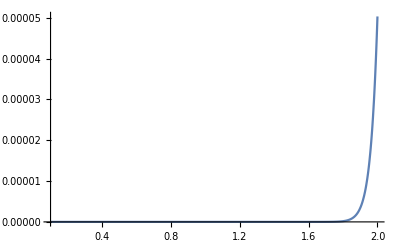

```mathematica
Plot[Subscript[B, pcart22][[3]]/.{d-> .2, zz->0, y->0}, {x, .1,2}, PlotRange->Full]
```

Re[ⅇ^(-12.5 ((3-r)^2+z^2)-2 ⅈ ϕ) (-1+r+ⅈ z)^2]

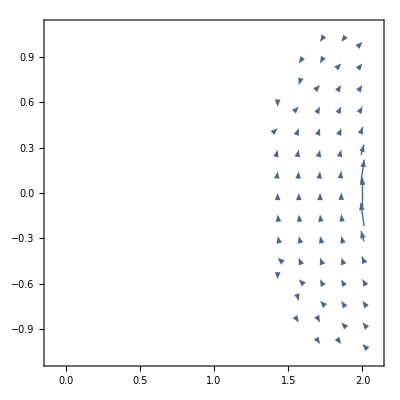

```mathematica
fn=Re[Subscript[ψ, pc22]]/.{ d->.2}
VectorPlot[{Subscript[B, pcart22][[1]]/.{d->.2, y->0},Subscript[B, pcart22][[3]]/.{d->.2, y->0}}, {x,0,2},{zz,-1,1}, PlotRange->Full]
Manipulate[ContourPlot[fn/.{ϕ->b}, {r,0,2},{z,-1,1}, PlotRange->Full], {b, 0, 2π}]
```

```mathematica
Subscript[ψ, pc]= Exp[-b^2/(2 d^2)]((r-1)+ⅈ z )^2 Exp[-ⅈ*3ϕ]
```

ⅇ^(-((3-r)^2+z^2)/(2 d^2)-3 ⅈ ϕ) (-1+r+ⅈ z)^2